# Least time path

```mathematica
expr1 = (√(1+y'[x]^2))/(√(-7/10 g y[x]))
```

(√(10/7) √(1+y'[x]^2))/(√(-g y[x]))

```mathematica
expr2 = D[expr1,y[x]]
```

(√(5/14) g √(1+y'[x]^2))/(-g y[x])^(3/2)

```mathematica
expr3 =D[expr1,y'[x]]
```

(√(10/7) y'[x])/(√(-g y[x]) √(1+y'[x]^2))

```mathematica
eq1 = Simplify[expr2 - D[expr3,x] == 0]
```

(g (1+y'[x]^2+2 y[x] y''[x]))/(√(-g y[x]) √(1+y'[x]^2))==0

Multiplying through  by √(-y[x]) √(1+y'[x]^2) we obtain:

```mathematica
eq2 = 1+y'[x]^2+2 y[x] y''[x] ==0
```

1+y'[x]^2+2 y[x] y''[x]==0

Claim: the solution is a cycloid, which is the graph that you would obtain if you tracked one point on a rolling wheel (in this case, we would roll the wheel on the ceiling). Let’s plot this with the “wheel” radius a = 2

```mathematica
xcomp = a(s-Sin[s])
ycomp = -a (1-Cos[s])
```

a (s-Sin[s])

-a (1-Cos[s])

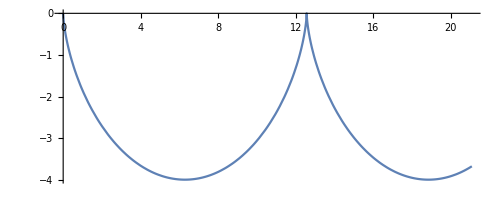

```mathematica
ParametricPlot[{xcomp,ycomp} /. {a -> 2},{s, 0, 10}]
```

Now consider using chain rule with the derivetive dy/ds = dy/dxdx/ds  so 
dy/dx =  (dy/ds)/(dx/ds) (1)
(d^2 y)/(d s^2)= d(dy/dx dx/ds)/ds = (d^2 y)/(d x^2)((d x)/(d s))^2+ dy/dx (d^2 x)/(d s^2)

(d^2 y)/(d s^2) = (d^2 y)/(d x^2)((d x)/(d s))^2+ (dy/ds)/(dx/ds)  (d^2 x)/(d s^2)
So (d^2 y)/(d x^2) = ((d^2 y)/(d s^2)  - (dy/ds)/(dx/ds)  (d^2 x)/(d s^2))/((d x)/(d s))^2 (2)

Next change the variables in the equation for the least time path:

```mathematica
eq3 = Simplify[eq2 /. { y''[x] -> (y''[s] - y'[s]/x'[s] x''[s])/(x'[s])^2, y'[x] -> y'[s]/x'[s],y[x] -> y[s]}]
```

x'[s]^2+y'[s]^2+2 y[s] y''[s]==(2 y[s] y'[s] x''[s])/x'[s]

Now plug the cycloid equations (1) and (2) into eq3 above to test if the solution works.

```mathematica
eq4 = eq3 /. {y[s] -> ycomp, y'[s] -> D[ycomp,s], y''[s] -> D[ycomp,s,s], x'[s] -> D[xcomp, s], x''[s] -> D[xcomp,s,s]}
```

a^2 (1-Cos[s])^2+2 a^2 (1-Cos[s]) Cos[s]+a^2 Sin[s]^2==2 a^2 Sin[s]^2

Finally simplifying we confirm that the solution is a cyclooid.

```mathematica
Simplify[eq4]
```

True

## Solution - cycloid. If the two points are (0,0) and (1, -0.5) we can adjust the parameter “a” to connect the two points with the cycloid. sf is the angle through which the wheel spins (we start at 0).

```mathematica
Clear[x,y]
```

```mathematica
Manipulate[Show[ParametricPlot[{a( s-Sin[ s]),-a (1-Cos[ s])} ,{s, 0, sf}] , ListPlot[{{0,0},{1,-0.5}}, PlotStyle -> Large], PlotRange -> All],{a,0.1,1}, {sf, 0.1, 10}]
```